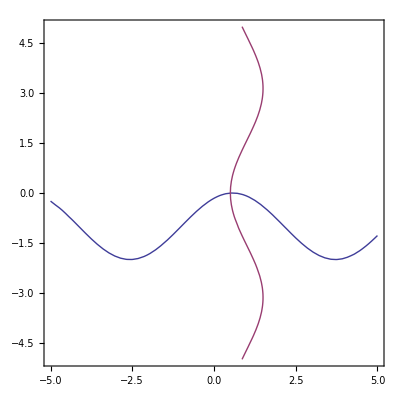

Cos[1+x] + Sin[y]/2

-Graphics-

x1 = 0.500001 -0.0025049

```mathematica
Clear[x];
Clear[y];
f=Sin[x + 1] - y - 1;
g = 2x + Cos[y] -2;

ContourPlot[{f ==0, g == 0},{x,-5,5}, {y, -5,5}]
ϕ1 = -1 +Sin[x + 1];
ϕ2 = 1 - Cos[y]/2;
derPhi1 = D[ϕ1,x];
derPhi2 = D[ϕ2,y];
Print[derPhi1, " + ",derPhi2];
Plot[Abs[derPhi1]+ Abs[derPhi2], {x,-3,3}]
checkTheorem[f_,segm_]:=(
Clear[x];
Clear[y];
delta = Abs[segm[[2]]-segm[[1]]]/2;
x0=segm[[2]]-delta;
derF1=D[f,x];
Print[ derF1];
x = segm[[1]];
q=  Abs[derF1];
x=x0;
Print["q = ",q ];
Print["q < 1 - ",q < 1];
m = Abs[x0 - f];
Print["m/(1  -  q) ",m/(1 - q) ];
Print["delta - ", delta];

Print["m/(1  -  q) <= delta - ",m/(1 - q) <= delta];

Return[x0];
);

defineRoot[f_, startx_, endx_, starty_, endy_] := (
Clear[x];
Clear[y];
deltax = (endx-startx)/2;
x00=endx-deltax;
deltay = (endy-starty)/2;
y00=endy-deltay;
yn = y00;
xn = x00;
While[Abs[xn - x00] > 0.5 * 10^(-4)&& Abs[yn - y00] > 0.5 * 10^(-4) || xn == x00, 
	Clear[x];
	Clear[y];
         x00 = xn;
          x = x00;
         y00 = yn;
          y = y00;
	xn = ϕ2;
	yn =ϕ1;
         
];
Return[{xn, yn}];
);
x1 = defineRoot[ϕ,0, 2, -1,1];
Print["x1 = ", N[x1[[1]]], " ", N[x1[[2]]]];
Clear[x];
Clear[y];
```

```mathematica
N[Cos[1]+ 1/2*Sin[1]]
```

0.961038